```mathematica
m=1.;α=0.1;n=2;tf=100;p=2;
```

#### Original version

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t])),{i,n}]/.{x[0][t]:>x[1][t]-1,x[n+1][t]:>x[n][t]+1},Table[{x[i][0]==i,x[i]'[0]==RandomReal[{-1,1}]},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

#### Modified with initial position of all masses set to zero

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t])),{i,n}]/.{x[0][t]:>x[1][t],x[n+1][t]:>x[n][t]},Table[{x[i][0]==0.,x[i]'[0]==RandomReal[{-1,1}]},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

#### Modified with initial position of all masses set to e^(-i^2) and a normal distribution random velocity

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t])),{i,n}]/.{x[0][t]:>x[1][t],x[n+1][t]:>x[n][t]},Table[{x[i][0]==Exp[-i^2],x[i]'[0]==RandomReal[{-1,1}]},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

#### Modified with initial position of all masses set to e^(-i^2) and no velocity

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t])),{i,n}]/.{x[0][t]:>x[1][t],x[n+1][t]:>x[n][t]},Table[{x[i][0]==Exp[-i^2],x[i]'[0]==0},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

#### Modified with first and last masses set to 0 position and other masses set to e^(-i^2) and no velocity

```mathematica
m=1.;α=0.25;n=32;tf=10000;p=2;b=0.0;a=1;
```

```mathematica
ic=Exp[-i^2];
ic = a Sin[π i/(n+1)];
(*ic = a Sin[π i n/(n+1)];*)
```

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t]))-b x[i]'[t],{i,n}]/.{x[0][t]:>0,x[n+1][t]:>0},Table[{x[i][0]==ic,x[i]'[0]==0.1},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

```mathematica
Table[nsol[[nparticle]][1],{nparticle,1,2}]
```

InterpolatingFunction[{{0., 100.}}, <>][Null]

```mathematica
Plot[Table[nsol[[i]][t], {i, 1,n}], {t, 0, tf}, 
       PlotRange -> All,  Frame -> True, Axes -> False, 
       ImageSize -> 100, AspectRatio -> 1]
```

-Graphics-

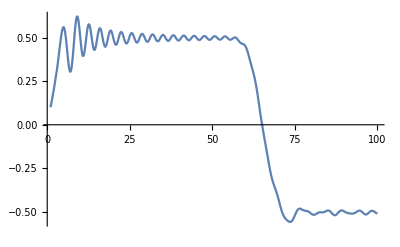

```mathematica
Plot[nsol[[5]][t],{t,1,tf}]
```

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-5,5}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]
```

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][tt]-nsol[[j-1]][tt],{j,2,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->14]
```

#### Comparison with Kuramoto - Sivashinsky

```mathematica
λ=1;a=1.;x0=20.;ν=1.;tmax=500.;

sol=NDSolveValue[{D[u[t,x],t]+λ D[u[t,x],x,x,x,x]+ν D[u[t,x],x,x]+u[t,x]D[u[t,x],x]==0,u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2) ,u[t,-x0]==u[t,x0]},u,{t,0,tmax},{x,-x0,x0},PrecisionGoal->2]
```

InterpolatingFunction[{{0., 500.}, {…, -20., 20., …}}, <>]

```mathematica
initialCond=Plot[ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2),{x,-20,20},PlotRange->All,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"X (space)","Amplitude","INITIAL CONDITION"}];
p3d=Plot3D[sol[x,y],{x,0.,tmax},{y,-x0,x0},MaxRecursion->1,Mesh->None,ColorFunction->ColorData["Rainbow"],PlotRange->Full,PlotPoints->100,BaseStyle->{FontSize->15},AxesLabel->{"T","  X","Wave profile,\n u(T,X)"},ImageSize->600,PlotLabel->"Evolution of initial condition \nper the Kuramoto-Sivashinky equation"];
```

```mathematica
Show[p3d]
```

-Graphics3D-

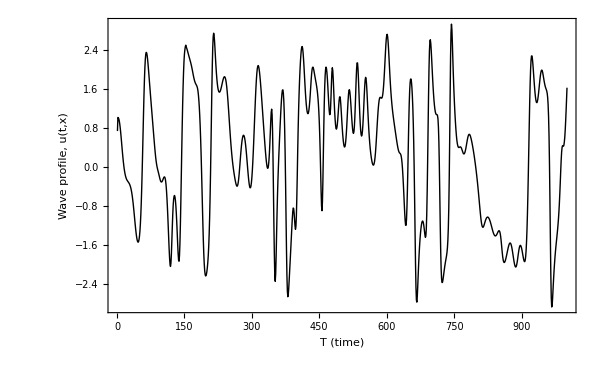

```mathematica
ks1=Table[sol[t,0],{t,0,tmax,tmax/1000}];

ListPlot[ks1,Joined->True,Frame->True,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"T (time)","Wave profile, u(t,x)"},LabelStyle->Black]
```